## Wannier bands in the QSH insulator

```mathematica
Clear["Global`*"]
MyMarker=Graphics[{Red,Circle[{0,0},1]}];

sx={{0,1},{1,0}};
sy={{0,-ⅈ},{ⅈ,0}};
sz={{1,0},{0,-1}};
s0={{1,0},{0,1}};
szsz = KroneckerProduct[sz,sz];
sxs0=KroneckerProduct[sx,s0];
s0sx=KroneckerProduct[s0,sx];
s0sy=KroneckerProduct[s0,sy];
s0sz=KroneckerProduct[s0,sz];

sxsy=KroneckerProduct[sx,sy];
szsx=KroneckerProduct[sz,sx];
sxsx=KroneckerProduct[sx,sx];
sysx=KroneckerProduct[sy,sx];

Hqsh[kx_,ky_,m_,δ_]:=(2-m-Cos[kx]-Cos[ky])s0sz+δ Sin[ky] sxsy + Sin[kx] (szsx+sxsx)+Sin[ky](sysx + s0sy)
```

```mathematica
ExpToTrig[Hqsh[kx,ky,m,d]]//MatrixForm
```

(2-m-Cos[kx]-Cos[ky] | Sin[kx]-ⅈ Sin[ky] | 0 | Sin[kx]-ⅈ Sin[ky]-ⅈ d Sin[ky]
Sin[kx]+ⅈ Sin[ky] | -2+m+Cos[kx]+Cos[ky] | Sin[kx]-ⅈ Sin[ky]+ⅈ d Sin[ky] | 0
0 | Sin[kx]+ⅈ Sin[ky]-ⅈ d Sin[ky] | 2-m-Cos[kx]-Cos[ky] | -Sin[kx]-ⅈ Sin[ky]
Sin[kx]+ⅈ Sin[ky]+ⅈ d Sin[ky] | 0 | -Sin[kx]+ⅈ Sin[ky] | -2+m+Cos[kx]+Cos[ky])

## Energy bands

```mathematica
Np=81;
m=0.5;
d=0.5;
ListPlot3D[Table[Table[Sort[Eigenvalues[Hqsh[kx,ky,m,d]]][[i]],{kx,-π,π,2π/(Np+1)},{ky,-π,π,2π/(Np+1)}],{i,1,4}],AspectRatio->1]
```

-Graphics3D-

## Subspace of occupied bands

```mathematica
kx=0;
ky=π/2;
Eigensystem[Hqsh[kx,ky,m,d]]
```

{{1.97844,-1.97844,1.04201,-1.04201},{{-5.02416×10^-17+0.731187 ⅈ,-0.233919-2.72796×10^-17 ⅈ,0.+0.302867 ⅈ,-0.56473+0. ⅈ},{1.95674×10^-17+0.56473 ⅈ,0.302867-2.10693×10^-17 ⅈ,0.+0.233919 ⅈ,0.731187+0. ⅈ},{3.80769×10^-17-0.329179 ⅈ,0.47116+1.49878×10^-16 ⅈ,-1.94289×10^-16+0.794709 ⅈ,-0.195161+0. ⅈ},{-9.6573×10^-17-0.195161 ⅈ,-0.794709+8.88581×10^-17 ⅈ,2.77556×10^-17+0.47116 ⅈ,0.329179+0. ⅈ}}}

```mathematica
Transpose[Eigensystem[Hqsh[kx,ky,m,d]]]
```

{{1.97844,{-5.02416×10^-17+0.731187 ⅈ,-0.233919-2.72796×10^-17 ⅈ,0.+0.302867 ⅈ,-0.56473+0. ⅈ}},{-1.97844,{1.95674×10^-17+0.56473 ⅈ,0.302867-2.10693×10^-17 ⅈ,0.+0.233919 ⅈ,0.731187+0. ⅈ}},{1.04201,{3.80769×10^-17-0.329179 ⅈ,0.47116+1.49878×10^-16 ⅈ,-1.94289×10^-16+0.794709 ⅈ,-0.195161+0. ⅈ}},{-1.04201,{-9.6573×10^-17-0.195161 ⅈ,-0.794709+8.88581×10^-17 ⅈ,2.77556×10^-17+0.47116 ⅈ,0.329179+0. ⅈ}}}

```mathematica
SortBy[Transpose[Eigensystem[Hqsh[kx,ky,m,d]]],First]
```

{{-1.97844,{1.95674×10^-17+0.56473 ⅈ,0.302867-2.10693×10^-17 ⅈ,0.+0.233919 ⅈ,0.731187+0. ⅈ}},{-1.04201,{-9.6573×10^-17-0.195161 ⅈ,-0.794709+8.88581×10^-17 ⅈ,2.77556×10^-17+0.47116 ⅈ,0.329179+0. ⅈ}},{1.04201,{3.80769×10^-17-0.329179 ⅈ,0.47116+1.49878×10^-16 ⅈ,-1.94289×10^-16+0.794709 ⅈ,-0.195161+0. ⅈ}},{1.97844,{-5.02416×10^-17+0.731187 ⅈ,-0.233919-2.72796×10^-17 ⅈ,0.+0.302867 ⅈ,-0.56473+0. ⅈ}}}

```mathematica
SortBy[Transpose[Eigensystem[Hqsh[kx,ky,m,d]]],First][[1;;2]]
```

{{-1.97844,{1.95674×10^-17+0.56473 ⅈ,0.302867-2.10693×10^-17 ⅈ,0.+0.233919 ⅈ,0.731187+0. ⅈ}},{-1.04201,{-9.6573×10^-17-0.195161 ⅈ,-0.794709+8.88581×10^-17 ⅈ,2.77556×10^-17+0.47116 ⅈ,0.329179+0. ⅈ}}}

```mathematica
Transpose[SortBy[Transpose[Eigensystem[Hqsh[kx,ky,m,d]]],First][[1;;2]]][[2]]
```

{{1.95674×10^-17+0.56473 ⅈ,0.302867-2.10693×10^-17 ⅈ,0.+0.233919 ⅈ,0.731187+0. ⅈ},{-9.6573×10^-17-0.195161 ⅈ,-0.794709+8.88581×10^-17 ⅈ,2.77556×10^-17+0.47116 ⅈ,0.329179+0. ⅈ}}

```mathematica
(*Alternatively*)
Transpose[SortBy[Transpose[Eigensystem[Hqsh[kx,ky,m,d]]],First]][[2,1;;2]]//MatrixForm
```

(1.95674×10^-17+0.56473 ⅈ | 0.302867-2.10693×10^-17 ⅈ | 0.+0.233919 ⅈ | 0.731187+0. ⅈ
-9.6573×10^-17-0.195161 ⅈ | -0.794709+8.88581×10^-17 ⅈ | 2.77556×10^-17+0.47116 ⅈ | 0.329179+0. ⅈ)

```mathematica
MatrixForm[u=Transpose[Transpose[SortBy[Transpose[Eigensystem[Hqsh[kx,ky,m,d]]],First]][[2,1;;2]]]]
```

(1.95674×10^-17+0.56473 ⅈ | -9.6573×10^-17-0.195161 ⅈ
0.302867-2.10693×10^-17 ⅈ | -0.794709+8.88581×10^-17 ⅈ
0.+0.233919 ⅈ | 2.77556×10^-17+0.47116 ⅈ
0.731187+0. ⅈ | 0.329179+0. ⅈ)

```mathematica
MatrixForm[P=u.ConjugateTranspose[u]]
```

(0.357007+0. ⅈ | 5.34337×10^-17+0.326134 ⅈ | 0.040149+3.55073×10^-17 ⅈ | -1.74824×10^-17+0.34868 ⅈ
5.34337×10^-17-0.326134 ⅈ | 0.723291+0. ⅈ | 1.48802×10^-17+0.303588 ⅈ | -0.040149+1.38446×10^-17 ⅈ
0.040149-3.55073×10^-17 ⅈ | 1.48802×10^-17-0.303588 ⅈ | 0.276709+0. ⅈ | 9.13656×10^-18+0.326134 ⅈ
-1.74824×10^-17-0.34868 ⅈ | -0.040149-1.38446×10^-17 ⅈ | 9.13656×10^-18-0.326134 ⅈ | 0.642993+0. ⅈ)

## Wilson loop and Wannier bands

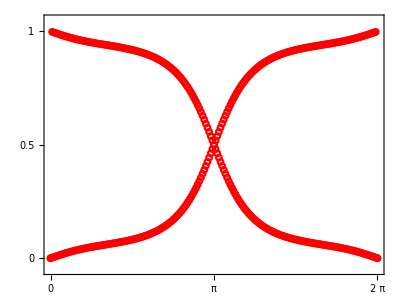
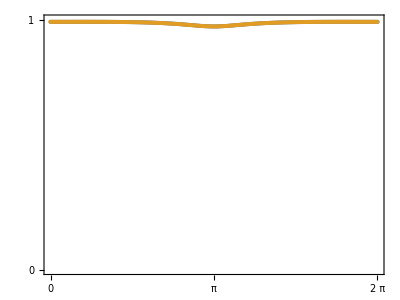

```mathematica
Nk=200;
(*m=5;(*trivial*)*)
m=3;(*QSH*)
δ=0;

kv=Table[N[i],{i,0,2π-2π/Nk,2π/Nk}];
uk=Table[Transpose[Transpose[SortBy[Transpose[Eigensystem[Hqsh[kv[[ki]],kv[[kj]],m,δ]]],First]][[2,1;;2]]],{ki,1,Nk},{kj,1,Nk}];
Pk=Table[uk[[ki,kj]].ConjugateTranspose[uk[[ki,kj]]],{ki,1,Nk},{kj,1,Nk}];
Wilson=Table[ConjugateTranspose[uk[[1,kj]]].(Dot@@Pk[[1;;Nk,kj]]).uk[[1,kj]],{kj,1,Nk}];
WilsonEig = Table[Eigenvalues[Wilson[[kj]]],{kj,1,Nk}];
WilsonEig =Append[WilsonEig ,WilsonEig [[1]]];

{ListPlot[Transpose[Mod[Arg[WilsonEig]/(2π),1]],
PlotStyle->{Blend[{Black,Blue},.5]},PlotMarkers->{MyMarker,.03},
DataRange->{0,2π},PlotRange->{{0,2π},{-0.05,1.05}},AxesOrigin->{0,0.5},
Frame->True,FrameTicks->{{0,π,2π},{0,0.5,1}},
AspectRatio->3/4,ImageSize->400],
ListPlot[Transpose[Abs[WilsonEig]],
DataRange->{0,2π},PlotRange->{{0,2π},{0,1}},
Frame->True,FrameTicks->{{0,π,2π},{0,1}},
AspectRatio->3/4,ImageSize->400]}
```